1)  set J and calc. (N̂)_ij^J and (Ĥ)_ij^J                      untainted/*.exe  boundstate with INQUA_N as in RHS calc.
2)

```mathematica
MUL=1;
jj =0;
mJ=0;
pi="-";
```

Setup of the RHS of the LIT equation  (Η̂-B_deu-σ_r-iσ_i) Ψ_LIT^Jm_J=[Ô Ψ_deu]^Jm_J  (which is a vector!)

Setup of the LHS of the LIT equation  (Η̂-B_deu-σ_r-iσ_i) Ψ_LIT^Jm_J=[Ô Ψ_deu]^Jm_J  

Read Norm  ( (Ν^J)_(l_n l_m))  and Hamilton  ( (Η^J)_(l_n l_m))  Matrix dimensionality for  J={0: N_1
1: N_0+N_1+N_2
2: N_1+N_2+N_3

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Append[LIToverlap,{{1,3.07992×10^-11-8.17164×10^-24 ⅈ},{499/100,5.99966×10^-11+1.57681×10^-24 ⅈ},{449/50,6.49004×10^-11-4.78214×10^-25 ⅈ},{1297/100,4.35993×10^-11+5.16988×10^-25 ⅈ},{424/25,4.13786×10^-11-3.55429×10^-25 ⅈ},{419/20,6.21536×10^-11+1.00813×10^-24 ⅈ},{1247/50,8.03698×10^-11-4.84676×10^-25 ⅈ},«37»,{4414/25,8.29887×10^-13-3.50355×10^-25 ⅈ},{3611/20,1.17232×10^-12+8.87033×10^-25 ⅈ},{9227/50,1.91731×10^-12+8.50379×10^-25 ⅈ},{18853/100,3.63676×10^-12-6.01921×10^-24 ⅈ},{4813/25,5.96685×10^-12+1.11258×10^-24 ⅈ},{19651/100,4.44824×10^-12-5.30329×10^-24 ⅈ},«49»}].

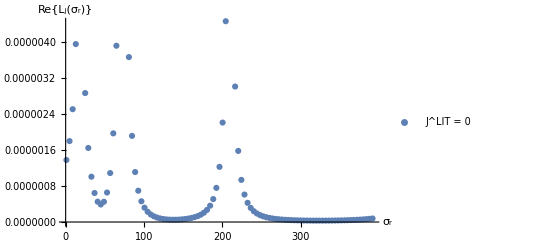

```mathematica
momentum=2;
sigmaI=5.5;smin=1;smax=400;nbrs=100;
sigmaRange=Range[smin,smax,(smax-smin)/nbrs];
file="/home_th/kirscher/kette_repo/source/ComptonLIT/av18_deuteron/norm-ham-litME-"<>ToString[jj]<>pi;
NormHamMat=ReadList[file,Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
file="/home_th/kirscher/kette_repo/source/ComptonLIT/av18_deuteron/LIT_SOURCE_"<>ToString[jj]<>pi<>ToString[mJ]<>ToString[MUL];
RHS=ReadList[file,Real,RecordLists->True];
Dimensions[norm];Dimensions[ham];
SlitDim=Dimensions[RHS[[1]]][[1]];
If[(JbasisDim==SlitDim)==False,
Print["Dim(Norm/H) ≠ Dim(S_LIT)"];
Print["Dim(Norm/H) = "<>ToString[JbasisDim]];
Print["Dim(S_LIT)   = "<>ToString[SlitDim]];
];
inhomo=RHS[[momentum]];
lOfSigma={};
For[n=1,n<nbrs,n++,(
(*Subscript[σ, r]=n;Subscript[σ, i]=5;σ=Subscript[σ, r]+I Subscript[σ, i];*)
coeff=LinearSolve[ham-Conjugate[sigmaRange[[n]]+sigmaI I] norm,inhomo];
lOfSigma=Append[lOfSigma,{sigmaRange[[n]],Conjugate[coeff].norm.coeff}];
)];
LIToverlap=Append[LIToverlap,lOfSigma];ListPlot[Re[lOfSigma],PlotLegends->{"J^LIT = "<>ToString[jj]},AxesLabel->{"σ_r","Re{L_j(σ_r)}"}](*,PlotRange->{0,10^(-6)}]*)
```

```mathematica
ϕ=Pi/3;
θ=Pi/3;
Plot[Re[expandedState[r Cos[θ] Sin[ϕ],r Sin[θ] Sin[ϕ],r Cos[ϕ],Lsets[[jj+1]],basisWidths,coeff]],{r,.01,6.5}]
```

```mathematica
basisWidths//MatrixForm
```

({12.9567,5.13467,2.939,1.69017,0.843,0.257369,0.13852,0.038519}
{0.444741,2.939,1.69017,1.18524,0.843,0.50011}
{0.444741,2.939,1.69017,1.18524,0.843,0.50011}
{0.444741,2.939,1.69017,1.18524,0.843,0.50011})

```mathematica
normmalcoeff=norm.coeff
normmalcoeff.coeff//MatrixForm
Conjugate[coeff].norm.coeff
```

{1.05785×10^-6+3.06049×10^-8 ⅈ,2.41402×10^-8+7.40847×10^-10 ⅈ,8.60316×10^-8+2.53363×10^-9 ⅈ,1.86044×10^-7+5.42301×10^-9 ⅈ,3.68715×10^-7+1.07022×10^-8 ⅈ,8.94637×10^-7+2.58962×10^-8 ⅈ}

1.36588×10^-12+7.91869×10^-14 ⅈ

1.36817×10^-12-1.31266×10^-27 ⅈ

```mathematica
ell=1;
m1=4;
m2=4;
(2 ell+1)!!/(2^(2+ell) (basisWidths[[ell+1]][[m1]]+basisWidths[[ell+1]][[m2]])^(1+ell)) Sqrt[Pi/(basisWidths[[ell+1]][[m1]]+basisWidths[[ell+1]][[m2]])]
```

0.0768279